# An evolutionary tipping point in a changing environment

## Preliminaries

For uniformity among figures

```mathematica
LabelSize=16; (*size of axis label text*)
FigureSize=400;  (*size of figure*)
TickSize=12;  (*size of tick text*)
Pad={{50,10},{40,10}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)
letpos={0.93,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.125,0.5};  (*relative location of y axis label position*)
LetterSize=20;  (*size of text in stability plots*)
```

Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*set current directory to be location of this file*)
imagedir="../IMAGES/";(*directory to save figures in*)
simdir="../../SIMULATIONS/"; (*directory with simulation results*)
```

Get package for plotting means with error bars

```mathematica
Needs["ErrorBarPlots`"]
```

## Continuous time

### Traditional fitness function (Lynch & Lande 1993)

#### Analytical treatment

Per capita growth rate (fitness) is a quadratic function of the difference between trait value, z, and the environmental optimum, θ, with stabilizing selection strength inversely related to σw

```mathematica
rTrad[z_]:=rm-(z-θ)^2/(2 σw^2)
```

Probability distribution of trait values in the population is normal with mean barg and variance σz^2

```mathematica
p[z_]:=PDF[NormalDistribution[barg,σz],z]
```

Population mean fitness is then

```mathematica
barrTrad=Collect[Integrate[rTrad[z]p[z],{z,-∞,∞},Assumptions->{σz>0,σw>0}],rm]
```

rm-((barg-θ)^2+σz^2)/(2 σw^2)

The deterministic rate of change in the mean trait value (rate of evolution) is

```mathematica
dbargdtTrad=σg^2 D[barrTrad,barg]
```

-((barg-θ) σg^2)/σw^2

With uncertainty in the optimum (stochastic environment) and genetic drift, the rate of evolution is

```mathematica
dbargdtTrad+ϵg/.θ->k t + ϵθ
```

ϵg-((barg-k t-ϵθ) σg^2)/σw^2

The expected rate of change given barg and normally distributed genetic drift and noise in the optimum is

```mathematica
EdbargdtTrad=Simplify[Integrate[(dbargdtTrad+ϵg/.θ->k t + ϵθ)PDF[NormalDistribution[0,σθ],ϵθ]PDF[NormalDistribution[0,σdrift],ϵg],{ϵθ,-∞,∞},{ϵg,-∞,∞}],{σθ>0,σdrift>0}]
```

-((barg-k t) σg^2)/σw^2

The expected squared change is

```mathematica
Edbargdt2Trad=Simplify[Integrate[(dbargdtTrad+ϵg/.θ->k t + ϵθ)^2 PDF[NormalDistribution[0,σθ],ϵθ]PDF[NormalDistribution[0,σdrift],ϵg],{ϵθ,-∞,∞},{ϵg,-∞,∞}],{σθ>0,σdrift>0}]
```

(barg^2 σg^4-2 barg k t σg^4+k^2 t^2 σg^4+σdrift^2 σw^4+σg^4 σθ^2)/σw^4

And thus the variance in the rate of change is

```mathematica
Edbargdt2Trad-EdbargdtTrad^2//Simplify
```

σdrift^2+(σg^4 σθ^2)/σw^4

As described in Lande 1976 (in discrete time), with weak selection, the variance due to genetic drift (sampling of Ne parents with σg^2variance after selection) is σg^2/Ne, so we can write

```mathematica
VdbargdtTrad=Simplify[Edbargdt2Trad-EdbargdtTrad^2]/.σdrift^2->σg^2/Ne
```

σg^2/Ne+(σg^4 σθ^2)/σw^4

Note that the expected change in the lag x = k t - barg can be written

```mathematica
σg^2/σw^2(σw^2/σg^2(k-EdbargdtTrad)/.barg-k t->-x//Simplify)
```

(σg^2 (-x+(k σw^2)/σg^2))/σw^2

while the variance remains constant (σg^2/Ne+(σg^4 σθ^2)/σw^4 is independent of t and x). We thus have an Orstein-Uhlenbeck process with mean μ = (k σw^2)/σg^2, variance σ^2=σg^2/Ne+(σg^4 σθ^2)/σw^4, and constant θ=σg^2/σw^2). Thus the probability distribution of x at time t is normal with mean

```mathematica
meanxt=μ+(x0-x)Exp[-θ t]/.μ->(k σw^2)/σg^2/.x->k t-barg/.x0->0-barg0
```

ⅇ^(-t θ) (barg-barg0-k t)+(k σw^2)/σg^2

and variance

```mathematica
vbargt=VdbargdtTrad/(2θ)(1-Exp[-2 θ t])/.θ->(EdbargdtTrad/(k t-barg))// Simplify
```

-((-1+ⅇ^(-(2 t σg^2)/σw^2)) (σw^4+Ne σg^2 σθ^2))/(2 Ne σw^2)

So at equilbrium the distribution of barg is normal with mean

```mathematica
k t - meanxt/.ⅇ^(-t θ) ->0
```

k t-(k σw^2)/σg^2

and variance

```mathematica
Collect[vbargt/.ⅇ^(-(2 t σg^2)/σw^2)->0,Ne]
```

σw^2/(2 Ne)+(σg^2 σθ^2)/(2 σw^2)

The expected long-run population growth rate is then

```mathematica
Simplify[Integrate[barrTrad PDF[NormalDistribution[k t-(k σw^2)/σg^2,(σw^2/(2 Ne)+(σg^2 σθ^2)/(2 σw^2))^(1/2)],barg]PDF[NormalDistribution[k t,σθ],θ],{barg,-∞,∞},{θ,-∞,∞}],{σθ>0,σw>0,Ne>0,σg>0}];
ErTrad=Collect[%//Expand,{σθ^2}]
```

-1/(4 Ne)+rm-(k^2 σw^2)/(2 σg^4)-σz^2/(2 σw^2)+(-σg^2/(4 σw^4)-1/(2 σw^2)) σθ^2

and the critical rate of environmental change is

```mathematica
kcTrad=Solve[0==ErTrad,k][[2]]
```

{k→(σg^2 √(-σw^4+4 Ne rm σw^4-2 Ne σw^2 σz^2-Ne σg^2 σθ^2-2 Ne σw^2 σθ^2))/(√2 √Ne σw^3)}

So with an infinitely large population in a deterministic environment the critical rate is

```mathematica
Simplify[Limit[k/.kcTrad,Ne->∞]/.σθ^2->0,σw>0]
```

(σg^2 √(2 rm σw^2-σz^2))/σw^2

### Alternative fitness function

#### Analytical treatment

Per capita growth rate (fitness) as a Gaussian function

```mathematica
rAlt[z_]:=rm-d(1-Exp[-(z-θ)^2/(2 σw^2)])
```

This alternative fitness function is equivalent to the traditional fitness function, to second order, when the lag is small and d=0

```mathematica
rTrad[z]==Normal[Series[rAlt[z],{z,θ,2}]]/.d->1
```

True

Probability distribution of trait values in the population is normal with mean barg and variance σz^2

```mathematica
p[z_]:=PDF[NormalDistribution[barg,σz],z]
```

Population mean fitness is then

```mathematica
barrAlt=Collect[Integrate[rAlt[z]p[z],{z,-∞,∞},Assumptions->{σz>0,σw>0}],rm]
```

rm+d (-1+(ⅇ^(-(barg-θ)^2/(2 (σw^2+σz^2))) σw)/(√(σw^2+σz^2)))

This has a maximum of (and approximation under weak selection)

```mathematica
barrAlt/.barg->θ
Simplify[Normal[Series[%/.σw->σw/ϵ^(1/2),{ϵ,0,0}]],σw>0]
```

rm+d (-1+σw/(√(σw^2+σz^2)))

rm

and a minimum of

```mathematica
Limit[barrAlt/.barg->θ-L,L->∞,Assumptions->{σw>0,σz>0}]
```

-d+rm

The deterministic rate of change in the trait value (rate of evolution) is

```mathematica
dbargdtAlt=σg^2 D[barrAlt,barg]
```

-(d ⅇ^(-(barg-θ)^2/(2 (σw^2+σz^2))) (barg-θ) σg^2 σw)/((σw^2+σz^2)^(3/2))

With uncertainty in the optimum (stochastic environment) and genetic drift the rate of evolution is

```mathematica
dbargdtAlt+ϵg/.θ->k t + ϵθ
```

ϵg-(d ⅇ^(-(barg-k t-ϵθ)^2/(2 (σw^2+σz^2))) (barg-k t-ϵθ) σg^2 σw)/((σw^2+σz^2)^(3/2))

The expected rate of change given barg and normally distributed genetic drift and noise in the optimum is

```mathematica
EdbargdtAlt=Simplify[Integrate[(dbargdtAlt+ϵg/.θ->k t + ϵθ)PDF[NormalDistribution[0,σθ],ϵθ]PDF[NormalDistribution[0,σdrift],ϵg],{ϵθ,-∞,∞},{ϵg,-∞,∞}],{σθ>0,σdrift>0,σw>0,σz>0}]
```

-(d ⅇ^(-(barg-k t)^2/(2 (σw^2+σz^2+σθ^2))) (barg-k t) σg^2 σw)/((σw^2+σz^2+σθ^2)^(3/2))

The expected change is no longer linear in barg and the variance is no longer independent of barg or time, thus we cannot use the Orstein-Uhlenbeck results as we could for the traditional fitness function results. Instead we focus on the expected rate of evolution.

Note that there is a maximum in the expected rate of evolution at lag

```mathematica
Solve[0==D[EdbargdtAlt/.barg-k t->-L,L],L][[2]]
```

{L→√(σw^2+σz^2+σθ^2)}

The maximum rate of evolution is

```mathematica
ktip=EdbargdtAlt/.barg-k t->-L/.%/.σw^2+σz^2+σθ^2->V
```

(d σg^2 σw)/(√ⅇ V)

As long as the rate of environmental change is less than the maximum rate of evolution, the steady-state lag is

```mathematica
eqLAlt=Solve[EdbargdtAlt==k/.barg-k t->-L,L][[1]]/.σw^2+σz^2+σθ^2->V
(*%/.σg->1/.σw->1/.rm->1.1/.σz->2/.σθ->1/.k->0.01*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{L→-ⅈ √V √ProductLog[-(k^2 V^2)/(d^2 σg^4 σw^2)]}

This is only biologically valid (real) when

```mathematica
Reduce[x>0&&ProductLog[-x]<0,x,Reals]/.x->(k^2 V^2)/(d^2 σg^4 σw^2)
```

0<(k^2 V^2)/(d^2 σg^4 σw^2)≤1/ⅇ

i.e., when the rate of change in the environment is less than the maximum rate of evolution (as stated just above).

The long-run population growth rate, as long as the steady-state lag is valid, is then

```mathematica
barreqAlt=barrAlt/.barg-θ->L/.eqLAlt
```

rm+d (-1+(ⅇ^((V ProductLog[-(k^2 V^2)/(d^2 σg^4 σw^2)])/(2 (σw^2+σz^2))) σw)/(√(σw^2+σz^2)))

Because this is a decreasing function of the rate of environmental change over its biologically valid range, the minimum value this can take on is

```mathematica
barreqAlt/.k->ktip
```

rm+d (-1+(ⅇ^(-V/(2 (σw^2+σz^2))) σw)/(√(σw^2+σz^2)))

When this minimum is less than zero we know that the population mean growth rate becomes zero before the maximum rate of evolution is reached, and thus there is a critical rate of environmental change. If, however, the population growth rate at the maximum rate of evolution is greater than zero then there is no critical rate of environmental change, as typically defined, and it is the maximum rate of evolution that determines persistence (as long as extinction is possible, rm-d<0). For this latter scenario of no critical rate we therefore need rm<d and

```mathematica
Reduce[σw>0&&σz>0&&V>0&&0<rm&&0<d&&0<barreqAlt/.k->ktip,rm,Reals]
```

σw≠0&&d>0&&V>0&&σw>0&&σz>0&&rm>d-√((d^2 ⅇ^(-V/(σw^2+σz^2)) σw^2)/(σw^2+σz^2))

Or, with weak selection,

```mathematica
Reduce[σw>0&&σz>0&&V>0&&0<rm<d&&0<d&&0<Normal[Series[barreqAlt/.k->ktip/.V->σw^2+σz^2+σe^2/.σw->σw/ϵ^(1/2),{ϵ,0,0}]],rm,Reals]
%//N
```

V>0&&σz>0&&σw>0&&d>0&&(-d+d √ⅇ)/(√ⅇ)<rm<d

V>0.&&σz>0.&&σw>0.&&d>0.&&0.393469 d<rm<d

When d<rm the population never goes extinct, when (-d+d √ⅇ)/(√ⅇ)<rm<d the maximum rate of evolution determines persistence, and when rm<(-d+d √ⅇ)/(√ⅇ) the critical rate would be

```mathematica
Simplify[Solve[0==barreqAlt,k][[2]],{σθ>0,σw>0,σg>0,σz>0,rm>0,d>0}]
(*%/.σg->1/.σw->1/.rm->0.9/.σz->2/.σθ->0*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→√2 d σg^2 σw √(-((((d-rm) √(σw^2+σz^2))/(d σw))^((2 (σw^2+σz^2))/V) (σw^2+σz^2) Log[((d-rm) √(σw^2+σz^2))/(d σw)])/V^3)}

### Figure 1 (A-D): steady-state lag and long-run population mean growth rate as functions of the rate of environmental change

```mathematica
GrowthLag=
Legended[
Show[
Plot[barrTrad/.rm->Log[B]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg,{L,0,4.5},AxesOrigin->{0,0},PlotStyle->{Gray,Thick}],
Plot[barrAlt/.rm->Log[B]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,{L,0,10},Axes->False,PlotStyle->{Black,Thick}],
(*Plot[0,{L,-10,10},PlotStyle->Black],*)
PlotRange->{{0,10},{-0.5,0.8}},
Frame->False,
PlotRangePadding->None,
FrameLabel->{Style["",LabelSize],Style["",LabelSize]},
ImageSize->FigureSize,
ImagePadding->Pad,
AxesStyle->Directive[FontSize->TickSize],
TicksStyle->{{FontColor->White,Black},{Black,Black}},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@{0.05,0.95}],
Rotate[Text[Style["Population growth rate",LabelSize],Scaled@ylabpos],90 Degree](*,
Text[Style["Traditional",LabelSize],Scaled@{0.5,1}]*)
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.2]],
Directive[Black,Thickness[0.2]]
},
{
Style["Traditional",LabelSize],
Style["Alternative",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"(*,
LegendLabel->"Fitness function"*)
],
Scaled@{0.8,0.9}
]
];
```

```mathematica
SelectionLag=Show[Plot[D[barrTrad,barg]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,{L,0,4.25},AxesOrigin->{0,0},PlotStyle->{Gray,Thick}],
Plot[D[barrAlt,barg]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,{L,0,10},Axes->False,PlotStyle->{Black,Thick}],
koverV=0.15;
Plot[koverV,{L,0,10},PlotStyle->{Black,Dashed}],
Graphics[{PointSize[0.03],Gray,Point[{
L/.Solve[koverV==D[barrTrad,barg]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,L][[1]],
koverV
}]}],
Graphics[{PointSize[0.03],Black,Point[{
L/.Solve[koverV==D[barrAlt,barg]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,L][[1]],
koverV
}]}],
ListPlot[{{
L/.Solve[koverV==D[barrAlt,barg]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1,L][[2]],
koverV
}},
PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->10]
],
PlotRange->{{0,10},{0,0.5}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Mean phenotypic lag",LabelSize],Style["",LabelSize]},
ImageSize->FigureSize,
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Black}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@{0.05,0.95}],
Rotate[Text[Style["Selection gradient",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["k/σ_g^2",LabelSize],{9.8,0.125}]
},
PlotRangeClipping->False
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
SSLag=Show[
Plot[(k σw^2)/σg^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.B->2/.σw->9^(1/2)/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2),{k,0,0.1},PlotStyle->{Gray,Thick}],
Plot[L/.eqLAlt/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+1/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.B->2/.σw->9^(1/2)/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.σθ->0/.d->1,{k,0,0.1},PlotStyle->{Black,Thick}],
ParametricPlot[{σg^2 D[barrAlt,barg]/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+1/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.B->2/.σw->9^(1/2)/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.σθ->0/.d->1/.θ->barg+L,L},{L,0,10},PlotStyle->{Black,Thick,Dashing[Large]}],
Graphics[Arrow[{{ktip/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.σθ->0/.σw->ω/.ω->3/.d->1,6.5},{ktip/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.σθ->0/.σw->ω/.ω->3/.d->1,4}}]],
PlotRange->{{0,0.1},{0,10}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["",LabelSize],Style["",LabelSize]},
ImageSize->FigureSize,
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@{0.05,0.95}],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Evolutionary tipping point",LabelSize],{0.05,7}]
},
PlotRangeClipping->False
];
```

```mathematica
SSgrowth=Show[
Plot[ErTrad/.σz^2->σg^2+1/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.rm->Log[B]/.B->2/.σθ->0/.σw->9^(1/2)/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2),{k,0,0.0925},PlotStyle->{Gray,Thick},PlotRange->{-1,1}],
Plot[barreqAlt/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+1/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.rm->Log[B]/.B->2/.σθ->0/.σw->9^(1/2)/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.d->1,{k,0,0.1},PlotStyle->{Black,Thick},PlotRange->{-1,1}],
Plot[barrAlt/.rm->Log[B]/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.θ->L+barg/.σw->ω/.ω->3/.θ->L+barg/.d->1/.L->∞,{k,ktip/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.σθ->0/.σw->ω/.ω->3/.d->1,0.1},PlotStyle->{Black,Thick},PlotRange->{-1,1}],
Graphics[{Gray,Arrow[{{k/.kcTrad/.rm->Log[B]/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.σθ->0/.σw->ω/.ω->3/.d->1,0.6},{k/.kcTrad/.rm->Log[B]/.V->σw^2+σz^2+σθ^2/.σz^2->σg^2+σe^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->σw^2+1/.Ne->(2B)/(2B-1)KK/.KK->128/.n->50/.μ->2*10^-4/.α->0.05^(1/2)/.B->2/.σe^2->1/.σθ->0/.σw->ω/.ω->3/.d->1,0.05}}]}],
PlotRange->{{0,0.1},{-0.5,0.8}},
Frame->{False,False,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize]},
ImageSize->FigureSize,
ImagePadding->Pad,
AxesStyle->Directive[FontSize->TickSize],
TicksStyle->{{Black,Black},{Black,Black}},
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@{0.05,0.95}],
Rotate[Text[Style["Long-run population growth rate",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Rate of environmental change",LabelSize],Scaled@{0.5,-0.15}],
Text[Style["Critical rate of environmental change",LabelSize,Gray],{0.06,0.65}]
},
PlotRangeClipping->False
];
```

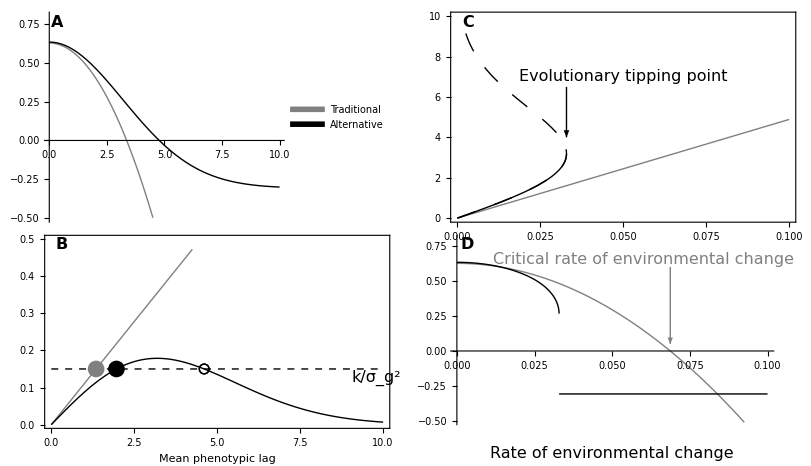

```mathematica
GraphicsGrid[{{GrowthLag,SSLag},{SelectionLag,SSgrowth}},Spacings->{0,-20}]
Export[imagedir<>"Didactics.pdf",%];
```

## Discrete time

### Traditional fitness function (Burger & Lynch 1995)

#### Analytical treatment

Probability of survival (fitness) as a Gaussian function of trait value, z, around optimum θ with standard deviation ω

```mathematica
W[z_]:= Exp[-(z-θ)^2/(2 ω^2)]
```

we then have equivalence with the continuous time traditional fitness funciton used above, exp(r(z)) = B W(z), where B is an integer determining the number of offspring per suriviving parent

```mathematica
Exp[rm-(z-θ)^2/(2 σw^2)]==B W[z]/.B->Exp[rm]/.σw->ω//Simplify
```

True

Probability distribution of trait values in the population is normal with mean barg and variance σz^2

```mathematica
p[z_]:=PDF[NormalDistribution[barg,σz],z]
```

Population mean fitness is then

```mathematica
barW=Integrate[W[z]p[z],{z,-∞,∞},Assumptions->{σz>0,ω>0}]
```

(ⅇ^(-(barg-θ)^2/(2 (σz^2+ω^2))) ω)/(√(σz^2+ω^2))

The deterministic rate of change in the mean trait value (rate of evolution) is

```mathematica
dbarg=σg^2 D[Log[barW],barg]/.σz^2->σg^2+σe^2/.σe^2->Vs-ω^2
```

-((barg-θ) σg^2)/(Vs+σg^2)

Let f[ barg[t+1] | barg[t]] be the conditional distribution of the mean genetic value in the next generation given the mean genetic value in this generation. Following Lande 1976, given that selection is weak relative to the amount of additive genetic variance, ω^2>>σg^2, the distribution of genetic values of survivors of viability selection remains normal with mean barg + dbarg and variance σg^2. Taking a random sample of N_e values from this normal distribution (the parents), the conditional distribution of the mean genetic value of offspring in the next generation, given the mean genetic value and optimum in the last generation, is normal with expectation barg + dbarg and variance σg^2/N_e. The recursion for the unconditional distribution is then ϕ[barg[t+1]] = ∫ f[ barg[t+1] | barg[t]] ϕ[barg[t]] d barg[t]. With weak selection f is normal, and because ϕ[barg[0]] is a dirac (the initial state is given), ϕ is normal and hence completely determined by its mean and variance. Because this is a linear Gaussian process, the dynamics of the mean and variance are easily found.

The conditional distribution of the mean genetic value in the next generation given the current mean genetic value and current optimum is

```mathematica
f[bargnext_,barg_]:=PDF[NormalDistribution[barg+dbarg,(σg^2/Ne)^(1/2)],bargnext]
```

The unconditional distribution for the mean genetic value in the current generation (this remains normal) is

```mathematica
ϕ[barg_]:=PDF[NormalDistribution[μ,σ],barg]
```

Then the unconditional distribution for the mean genetic value in the next generation is

```mathematica
phinext=Simplify[Integrate[f[bargnext,barg] ϕ[barg],{barg,-∞,∞}],{σg>0,Vs>0,Ne>0,σ>0}]
```

(ⅇ^(-(Ne (Vs μ+θ σg^2-bargnext (Vs+σg^2))^2)/(2 (Ne Vs^2 σ^2+σg^2 (Vs+σg^2)^2))) (Vs+σg^2) √(Ne/(Ne Vs^2 σ^2+σg^2 (Vs+σg^2)^2)))/(√(2 π))

From this one can see that the expected mean genetic value changes from μ to μ+σg^2/(Vs+σg^2)(θ-μ) and the variance in the mean genetic value changes from σ^2 to (Vs/(Vs+σg^2))^2 σ^2+σg^2/Ne

Check:

```mathematica
Simplify[PDF[NormalDistribution[μ+σg^2/(Vs+σg^2)(θ-μ),((Vs/(Vs+σg^2))^2 σ^2+σg^2/Ne)^(1/2)],bargnext]/phinext,{Vs>0,σg>0,Ne>0,σ>0}]
```

1

We can then solve these recursions to get the mean and variance of the unconditional distribution for the mean genetic value (and thus the whole distribution) at any time t

```mathematica
meanrec=Collect[RSolve[{μ[t+1]==μ[t]+σg^2/(Vs+σg^2)(k t-μ[t]),μ[0]==μ0},μ[t],t],{μ0,t,k},Simplify]/.Vs/(Vs+σg^2)->1-s/.Vs+σg^2->σg^2/s
```

{{μ[t]→(k (-1+(1-s)^t))/s+k t+(1-s)^t μ0}}

```mathematica
Collect[RSolve[{V[t+1]==(Vs/(Vs+σg^2))^2 V[t]+σg^2/Ne,V[0]==V0},V[t],t],{V0},Simplify]/.Vs^2/((Vs+σg^2)^2)->(1-s)^2
```

{{V[t]→((1-s)^2)^t V0-((-1+((1-s)^2)^t) (Vs+σg^2)^2)/(Ne (2 Vs+σg^2))}}

If the optimum is also stochastic (an independent random normal variable with mean k t and variance σθ^2 in each generation) we have

```mathematica
phinext2=Simplify[Integrate[phinext PDF[NormalDistribution[k t,σθ],θ],{θ,-∞,∞}],{σg>0,Vs>0,Ne>0,σ>0,σθ>0}]
```

(ⅇ^(-(Ne (Vs μ+k t σg^2-bargnext (Vs+σg^2))^2)/(2 (σg^2 (Vs+σg^2)^2+Ne (Vs^2 σ^2+σg^4 σθ^2)))) (Vs+σg^2) √(Ne/(σg^2 (Vs+σg^2)^2+Ne (Vs^2 σ^2+σg^4 σθ^2))))/(√(2 π))

The change in the mean remains the same while the change in the variance alters a little, now σ^2 becomes (Vs/(Vs+σg^2))^2 σ^2+σg^2/Ne+(σg^2/(Vs+σg^2))^2 σθ^2. Check:

```mathematica
Simplify[PDF[NormalDistribution[μ+σg^2/(Vs+σg^2)(θ-μ),((Vs/(Vs+σg^2))^2 σ^2+σg^2/Ne+(σg^2/(Vs+σg^2))^2 σθ^2)^(1/2)],bargnext]/phinext2/.θ->k t,{Vs>0,σg>0,Ne>0,σ>0,σθ>0}]
```

1

The solution to the variance recursion is then

```mathematica
varrec=Collect[RSolve[{V[t+1]==(Vs/(Vs+σg^2))^2 V[t]+σg^2/Ne+(σg^2/(Vs+σg^2))^2 σθ^2,V[0]==V0},V[t],t],{V0,σθ^2},Simplify]/.Vs^2/((Vs+σg^2)^2)->(1-s)^2
```

{{V[t]→((1-s)^2)^t V0-((-1+((1-s)^2)^t) (Vs+σg^2)^2)/(Ne (2 Vs+σg^2))-((-1+((1-s)^2)^t) σg^2 σθ^2)/(2 Vs+σg^2)}}

as t becomes large the expected mean becomes

```mathematica
μ[t]/.meanrec/.(1-s)^t->0
```

{-k/s+k t}

and the variance in the mean becomes (and approximately given weak selection relative to genetic variance, Vs >> σg^2)

```mathematica
V[t]/.varrec/.((1-s)^2)^t->0
%/.Vs+σg^2->Vs/. 2 Vs+σg^2->2Vs
```

{((Vs+σg^2)^2)/(Ne (2 Vs+σg^2))+(σg^2 σθ^2)/(2 Vs+σg^2)}

{Vs/(2 Ne)+(σg^2 σθ^2)/(2 Vs)}

The expected population growth rate in generation t is then

```mathematica
Eλt=Simplify[B Integrate[(barW/.σz^2->σg^2+σe^2/.σe^2->Vs-ω^2) PDF[NormalDistribution[k t,σθ],θ]PDF[NormalDistribution[μ[t],V[t]^(1/2)],barg],{θ,-∞,∞},{barg,-∞,∞}],{σθ>0,Vs>0,σg>0,V[t]>0}]
```

(B ⅇ^(-(-k t+μ[t])^2/(2 (Vs+σg^2+σθ^2+V[t]))) ω)/(√(Vs+σg^2+σθ^2+V[t]))

which can be rewritten as in Burger & Lynch 1995 (equation 9). Check:

```mathematica
Simplify[Eλt/(B0( PDF[NormalDistribution[k t,Vλ^(1/2)],μ[t]] √(2 π Vλ))/.B0->(B  ω)/(√Vλ)/.Vλ->Vs+σg^2+σθ^2+V[t]),{σθ>0,Vs>0,σg>0,V[t]>0,Ne>0,ω>0,s>0}]
```

1

As time gets large the expected growth rate becomes

```mathematica
Eλ=Simplify[Eλt/.V[t]->((Vs+σg^2)^2)/(Ne (2 Vs+σg^2))+(σg^2 σθ^2)/(2 Vs+σg^2)/.μ[t]->-k/s+k t,{σθ>0,Vs>0,σg>0,V[t]>0,Ne>0,ω>0}]
```

B ⅇ^(-(k^2 Ne (2 Vs+σg^2))/(2 s^2 (Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) √((Ne (2 Vs+σg^2))/((Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) ω

The critical rate occurs where the expected growth rate as time gets large becomes 1

```mathematica
kc=Simplify[Solve[1==Eλ,k]/.C[1]->0,{σθ>0,Vs>0,σg>0,V[t]>0,Ne>0,ω>0}][[2]]
```

{k→(√2 √Log[B √((Ne (2 Vs+σg^2))/((Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) ω])/(√((Ne (2 Vs+σg^2))/(s^2 (Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))))}

This can be rewritten as in Burger & Lynch 1995 (equation 10). Check:

```mathematica
Simplify[(k/.kc)/(s √(2Vλ Log[B0])/.B0->(B  ω)/(√Vλ)/.Vλ->Vs+σg^2+σθ^2+V[t]/.V[t]->((Vs+σg^2)^2)/(Ne (2 Vs+σg^2))+(σg^2 σθ^2)/(2 Vs+σg^2)),{σθ>0,Vs>0,σg>0,V[t]>0,Ne>0,ω>0,s>0}]
```

1

### Alternative fitness function

#### Analytical treatment

An alternate function for the probability of survival (fitness)

```mathematica
W[z_]:= (1-dp)Exp[-d(1- Exp[-(θ-z)^2/(2 ω^2)])]
```

we then have equivalence with the continuous time alternative fitness funciton used above, exp(r(z)) = B W(z), when the probability of death of optimally adapted individuals is dp=0

```mathematica
Exp[rm-d(1-Exp[-(z-θ)^2/(2 σw^2)])]==B W[z]/.B->Exp[rm]/.σw->ω/.dp->0//Simplify
```

True

In discrete time the alternative fitness function (red) asymptotes at a higher value (when d<∞) than the traditionally used Gaussian fitness function (i.e., the probability of survival has some minimum greater than 0)

```mathematica
Limit[W[z]/.θ->L+z,L->∞,Assumptions->ω>0]
Limit[Exp[-(θ-z)^2/(2 ω^2)]/.θ->L+z,L->∞,Assumptions->ω>0]
```

-(-1+dp) ⅇ^-d

0

but is identical to second order when there is little lag, θ-z near 0, and d=1 and dp=0

```mathematica
Series[Exp[-(θ-z)^2/(2 ω^2)],{z,θ,2}]==Series[W[z],{z,θ,2}]/.d->1/.dp->0
```

True

In continuous time a bigger difference emerges: the alternative fitness function does not allow infinitely negative growth rates and its slope is bounded while the traditional Gaussian becomes ever more negative and ever more steep as trait values depart from the optimum

```mathematica
D[Log[B  Exp[-(θ-z)^2/(2 ω^2)]]/.θ->L+z,L]
Limit[D[Log[B Exp[-(θ-z)^2/(2 ω^2)]]/.θ->L+z,L],L->∞,Assumptions->{ω>0}]
D[Log[B W[z]]/.θ->L+z,L]
Limit[D[Log[B W[z]]/.θ->L+z,L],L->∞,Assumptions->{ω>0}]
```

-L/ω^2

-∞

-(d ⅇ^(-L^2/(2 ω^2)) L)/ω^2

0

The minimum expected number of offspring is

```mathematica
Limit[B W[z]/.θ->L+z,L->∞,Assumptions->ω>0]
```

-B (-1+dp) ⅇ^-d

which is below replacement as long as

```mathematica
Reduce[%<1&&1<B&&0<d&&0<dp<1,B,Reals]
```

d>0&&0<dp<1&&1<B<-ⅇ^d/(-1+dp)

With this more complicated function we are unable to integrate to get mean viability, but when phenotypic variation is small we can approximate mean viability by replacing z with the mean value of z in the fitness function, and the deterministic rate of evolution is then approximately

```mathematica
dbarg=σg^2 D[Log[W[barg]],barg]
```

(d ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2

Note that this has one maximum at over all positive lags

```mathematica
Solve[0==D[dbarg/.barg->θ-L,L],L]
```

{{L→-ω},{L→ω}}

The maximum rate of evolution is thus

```mathematica
dbarg/.barg->θ-L/.L->ω
```

(d σg^2)/(√ⅇ ω)

If this maximum rate of evolution is smaller than the critical rate then it is the one that determines persistence.

The steady-state lag is

```mathematica
leq=Solve[dbarg==k/.barg->θ-L,L][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{L→-ⅈ ω √ProductLog[-(k^2 ω^2)/(d^2 σg^4)]}

This becomes an imaginary number at the maximum rate of evolution

```mathematica
Solve[-1==ProductLog[-(k^2 ω^2)/(d^2 σg^4)],k]
```

{{k→-(d σg^2)/(√ⅇ ω)},{k→(d σg^2)/(√ⅇ ω)}}

Given the lag is real (i.e., the rate of environmental change is less than the maximum rate of evolution), the expected number of offspring per surviving offspring is

```mathematica
B W[z]/.θ->L+z/.leq
```

B (1-dp) ⅇ^(-d (1-ⅇ^(1/2 ProductLog[-(k^2 ω^2)/(d^2 σg^4)])))

The minimum value this can take on (while the lag is real) is

```mathematica
%/.%%[[2]]
```

B (1-dp) ⅇ^(-d (1-1/(√ⅇ)))

If this value is always above 1 then there is no critical rate of environmental change. i.e., there is no critical rate of environmental change when

```mathematica
Reduce[%>1&&1<B&&0<d&&0<dp<1,B,Reals]//Simplify
```

d>0&&0<dp<1&&B>ⅇ^(d-d/(√ⅇ))/(1-dp)

Recalling from above that we need B to be small enough such that the minimum expected number of offspring is below 1 (so that the population can go extinct), our condition for the maximum rate of evolution determining persistence (and thus the existence of a tipping point) is

```mathematica
Reduce[%%>1&&1<B<-ⅇ^d/(-1+dp)&&0<d&&0<dp<1,B,Reals]//Simplify
```

d>0&&0<dp<1&&ⅇ^(d-d/(√ⅇ))/(1-dp)<B<-ⅇ^d/(-1+dp)

For example, with d=1 and dp=0 the only value of B that creates an evolutionary tipping point is B=2

```mathematica
ⅇ^(d-d/(√ⅇ))/(1-dp)<B<-ⅇ^d/(-1+dp)/.d->1./.dp->0
```

1.48211<B<2.71828

### Simulation results

#### Figure 2 (A-E): summary (traditional)

```mathematica
(*parameter values*)
KK=512;
B=2;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
σθ=0;

(*crtical rate of change*)
kc=(√2 √Log[B √((Ne (2 Vs+σg^2))/((Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) ω])/(√((Ne (2 Vs+σg^2))/(s^2 (Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))));
kc1=kc/.s->σg^2/(σg^2+Vs)/.Vs->ω^2+1/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK;  (*crit rate with neutral gen var*)
kc2=kc/.s->σg^2/(σg^2+Vs)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK;  (*crit rate with SHC gen var*)
(*x limits*)
kmin=-0.005; 
kmax=Max[kc1,kc2];(*max critical rate*)

klist=Table[i * 0.01, {i,0,25}]; (*all rates of change simulated*)

repmax=9; (*number of reps minus 1*)
burngens=1000;
genmax=10000+burngens; (*last gen recorded for surviving reps*)

maxtpoints=10; (*max number of recorded timepoints to average over*)

(*directory with data*)
datadir=simdir<>"data6/";

(*simulation identifier*)
simname[k_,rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_k"<>ToString[NumberForm[k,{2,2}]]<>"_rep"<>ToString[rep]<>".csv";

(*expected growth rate*)
Eλ=B ⅇ^(-(k^2 Ne (2 Vs+σg^2))/(2 s^2 (Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) √((Ne (2 Vs+σg^2))/((Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) ω;
```

```mathematica
(*mean mean lag, over last 10 time steps*)
meanlagpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
phenos=Import[datadir<>"phenos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[k( gens[[-t]]-burngens)-Mean[phenos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

meanlagextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
phenos=Import[datadir<>"phenos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[k ( gens[[-t]]-burngens)-Mean[phenos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*genetic variance at last time step*)
genvarpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
genos=Import[datadir<>"genos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[Variance[genos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

genvarextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
genos=Import[datadir<>"genos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[Variance[genos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*popn growth rate before carrying capacity at last time step*)
rpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
ns=Import[datadir<>"n_"<>simname[k,rep]];
numparents=Import[datadir<>"numparents_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[ns[[1,-t]]/numparents[[1,-t]]-1//N,{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

rextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
ns=Import[datadir<>"n_"<>simname[k,rep]];
numparents=Import[datadir<>"numparents_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[ns[[1,-t]]/numparents[[1,-t]]-1//N,{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*percent reps extinct before end of simulation*)
percentextinct=Table[
{k,Mean[Table[
{
ns=Import[datadir<>"n_"<>simname[k,rep]];
If[ns[[1,Length[ns[[1]]]]]<2,1,0]
},
{rep,0,repmax}
]][[1]]},
{k,klist}
];

(*time to extinction given extinct*)
extincttime=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
If[x==genmax,Null,x-burngens]
},
{k,klist},
{rep,0,repmax}
];
```

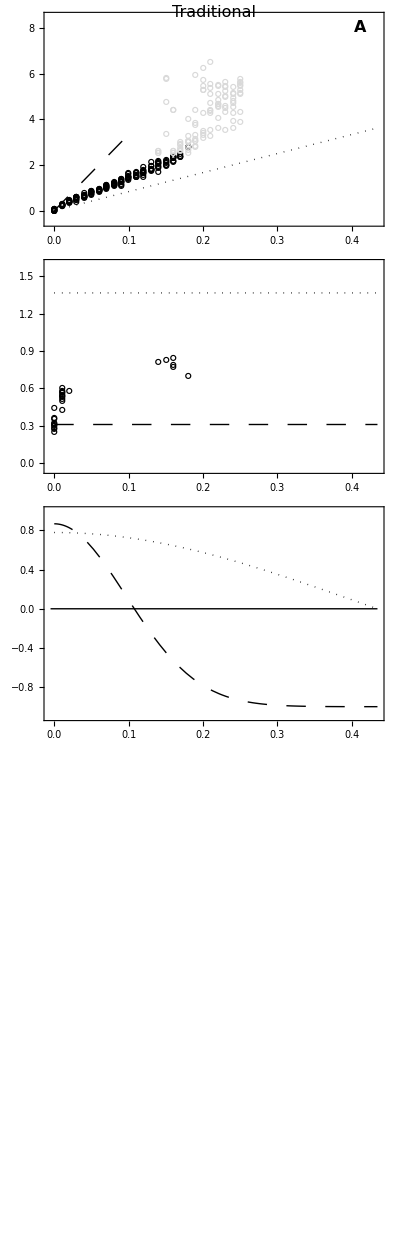

```mathematica
(*mean lag*)
lagtradplot=Show[
Plot[k/s/.s->σg^2/(σg^2+Vs)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kc2},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[k/s/.s->σg^2/(σg^2+Vs)/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kc1},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted},Axes->False],
ListPlot[
meanlagpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
meanlagextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-0.5,8.5}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Mean phenotypic lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Traditional",LabelSize],Scaled@{0.5,1}]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*genetic variance*)
vartradplot=Show[
Plot[σg^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,
{k,0,kmax},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[σg^2/.σg^2->4n μ α^2 Ne/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted}],
ListPlot[
genvarpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
genvarextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-0.05,1.6}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*popn growth rate*)
rtradplot=Show[
Plot[Eλ-1/.s->σg^2/(σg^2+Vs)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->All,PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[Eλ-1/.s->σg^2/(σg^2+Vs)/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->All,PlotStyle->{Black,Thick,Dotted}],
Plot[0,{k,kmin,kmax},PlotStyle->Black],
ListPlot[
rpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
rextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-1.1,1}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Population growth rate",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*percent extinct*)
percenttradplot=Show[
ListPlot[percentextinct,PlotMarkers->Style["•",20,Black],Axes->False],
PlotRange->{{kmin,kmax},{0,1.05}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Fraction extinct",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*mean time to extinction*)
timetradplot=Show[
ListPlot[extincttime,PlotMarkers->Style["∘",20,Black],PlotRange->{{0,kmax},{0,10200}}],
PlotRange->{{kmin,kmax},{-200,10200}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Generation extinct | extinct",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Black,Black}},
PlotRangeClipping->False
];

GraphicsGrid[{{lagtradplot},{vartradplot},{rtradplot},{percenttradplot},{timetradplot}},ImageSize->FigureSize,Spacings->0]

Export[imagedir<>"TradSummaryMeanLargeBurn.pdf",%];

Clear[KK,B,ω,μ,α,n,σθ]
```

#### Figure 2 (F-J): summary (alternative)

```mathematica
(*parameter values*)
KK=512;
B=2;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
σθ=0;

kc=(√2 √Log[B √((Ne (2 Vs+σg^2))/((Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))) ω])/(√((Ne (2 Vs+σg^2))/(s^2 (Vs+σg^2) (Vs+2 Ne Vs+(1+Ne) σg^2+2 Ne σθ^2))));(*critical rate*)
kc1=σg^2/(√ⅇ ω)/.s->σg^2/(σg^2+Vs)/.Vs->ω^2+1/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK;  (*tip pt with neutral gen var*)
kc2=σg^2/(√ⅇ ω)/.s->σg^2/(σg^2+Vs)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK;  (*tip pt with SHC gen var*)
kc3=kc/.s->σg^2/(σg^2+Vs)/.Vs->ω^2+1/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK;  (*crit rate with neutral gen var*)
kc4=kc/.s->σg^2/(σg^2+Vs)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK;  (*crit rate with SHC gen var*)
(*x limits*)
kmin=-0.005; 
kmax=Max[kc3,kc4];(*max critical rate*)

klist=Table[i * 0.01, {i,0,25}]; (*all rates of change simulated*)

repmax=9; (*number of reps minus 1*)
burngens=1000;
genmax=10000+burngens; (*last gen recorded for surviving reps*)

maxtpoints=10; (*max number of recorded timepoints to average over*)

(*directory with data*)
datadir=simdir<>"altdata5/";

(*simulation identifier*)
simname[k_,rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_k"<>ToString[NumberForm[k,{2,3}]]<>"_rep"<>ToString[rep]<>".csv";

(*expected growth rate*)
Eλ=B Exp[-(1-Exp[-(θ-z)^2/(2 ω^2)])]/.θ->L+z/.L->-ⅈ ω √ProductLog[-(k^2 ω^2)/(d^2 σg^4)]/.d->1;
```

```mathematica
(*mean mean lag, over last 10 time steps*)
meanlagpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
phenos=Import[datadir<>"phenos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[k( gens[[-t]]-burngens)-Mean[phenos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

meanlagextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
phenos=Import[datadir<>"phenos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[k ( gens[[-t]]-burngens)-Mean[phenos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*genetic variance at last time step*)
genvarpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
genos=Import[datadir<>"genos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[Variance[genos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

genvarextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
genos=Import[datadir<>"genos_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[Variance[genos[[-t]]],{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*popn growth rate before carrying capacity at last time step*)
rpersist=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
ns=Import[datadir<>"n_"<>simname[k,rep]];
numparents=Import[datadir<>"numparents_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x<genmax,Null,Mean[Table[ns[[1,-t]]/numparents[[1,-t]]-1//N,{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

rextinct=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
ns=Import[datadir<>"n_"<>simname[k,rep]];
numparents=Import[datadir<>"numparents_"<>simname[k,rep]];
tpoints=Min[maxtpoints,Length[gens]];
If[x==genmax,Null,Mean[Table[ns[[1,-t]]/numparents[[1,-t]]-1//N,{t,1,tpoints}]]]
},
{k,klist},
{rep,0,repmax}
];

(*percent reps extinct before end of simulation*)
percentextinct=Table[
{k,Mean[Table[
{
ns=Import[datadir<>"n_"<>simname[k,rep]];
If[ns[[1,Length[ns[[1]]]]]<2,1,0]
},
{rep,0,repmax}
]][[1]]},
{k,klist}
];

(*time to extinction given extinct*)
extincttime=
Table[{
k,
gens=Import[datadir<>"gens_"<>simname[k,rep]];
gens=Select[gens[[1]],#>burngens&];
x=gens[[-1]];
If[x==genmax,Null,x-burngens]
},
{k,klist},
{rep,0,repmax}
];
```

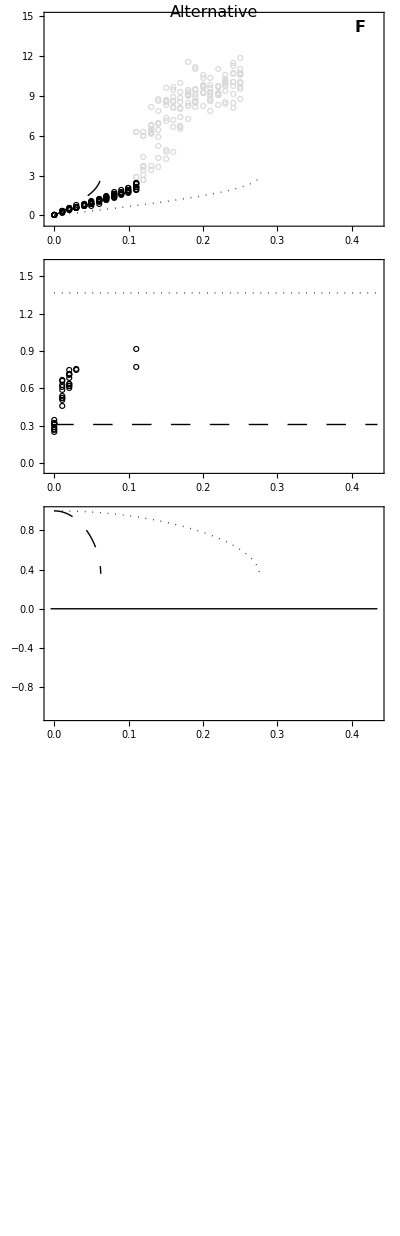

```mathematica
(*mean lag*)
lagaltplot=Show[
Plot[ ω √(-ProductLog[-(k^2 ω^2)/σg^4])/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kc2},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]}],
Plot[ ω √(-ProductLog[-(k^2 ω^2)/σg^4])/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kc1},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted}],
ListPlot[
meanlagpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
meanlagextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-0.5,15}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Alternative",LabelSize],Scaled@{0.5,1}]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*genetic variance*)
varaltplot=Show[
Plot[σg^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,
{k,0,kmax},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[σg^2/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted}],
ListPlot[
genvarpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
genvarextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-0.05,1.6}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["G",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*popn growth rate*)
raltplot=Show[
Plot[Eλ-1/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->All,PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[Eλ-1/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{k,0,kmax},PlotRange->All,PlotStyle->{Black,Thick,Dotted}],
Plot[0,{k,kmin,kmax},PlotStyle->Black],
ListPlot[
rpersist,PlotMarkers->Style["∘",20,Black]
],
ListPlot[
rextinct,PlotMarkers->Style["∘",20,LightGray]
],
PlotRange->{{kmin,kmax},{-1.1,1}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["H",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*percent extinct*)
percentaltplot=Show[
ListPlot[percentextinct,PlotMarkers->Style["•",20,Black]],
PlotRange->{{kmin,kmax},{0,1.05}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["I",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*mean time to extinction*)
timealtplot=Show[
ListPlot[extincttime,PlotMarkers->Style["∘",20,Black],PlotRange->{{0,kmax},{0,10200}}],
PlotRange->{{kmin,kmax},{-200,10200}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["J",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
PlotRangeClipping->False
];

GraphicsGrid[{{lagaltplot},{varaltplot},{raltplot},{percentaltplot},{timealtplot}},ImageSize->FigureSize,Spacings->0]

Export[imagedir<>"AltSummaryMeanLargeBurn.pdf",%];

Clear[KK,B,ω,μ,α,n,rep,σθ,kmax]
```

#### Figure 3 (A-C): early warning signs over time series with increasing k (traditional)

```mathematica
Pad2={{50,50},{40,15}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)

(*parameter values*)
KK=512;
B=2;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
dk=0.000001;
σθ=0;
repmax=9;
burngens=1000;
totaltime=200000+burngens;

(*size of moving window; number of gens to calculate autocorr and var in mean lag over*)
window=30;

(*directory and sim name*)
Clear[sim]
datadir=simdir<>"datatimeseries3/";
sim[rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_dk"<>"0.000001"<>"_rep"<>ToString[rep]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[rep_]:=gens[rep]=Import[datadir<>"gens_"<>sim[rep]];
genos[rep_]:=genos[rep]=Import[datadir<>"genos_"<>sim[rep]];
phenos[rep_]:=phenos[rep]=Import[datadir<>"phenos_"<>sim[rep]];
ns[rep_]:=ns[rep]=Import[datadir<>"n_"<>sim[rep]];
numparents[rep_]:=numparents[rep]=Import[datadir<>"numparents_"<>sim[rep]];

(*number of recordings and max time*)
Clear[imax,tmax]
imax[rep_]:=imax[rep]=Length[gens[rep][[1]]];
tmax[rep_]:=tmax[rep]=gens[[1,imax[rep]]];
(*survivors of viability selection*)
(*Show[
Table[ListPlot[Table[{gens[rep][[1,i]],ns[rep][[1,i]]},{i,0,imax[rep],di}],Joined->True,PlotRange->{0,All},PlotStyle->Black],{rep,0,repmax}],
Plot[KK,{t,0,totaltime}(*,PlotStyle->{Thin}*),PlotStyle->Black],
Plot[(2B)/(2B-1)KK,{t,0,totaltime},PlotStyle->{Black,Thick}],
PlotRange->{{0,totaltime},All},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"","# survivors"}
]*)

(*mean lag and population growth rate*)
(*Show[
Table[ListPlot[
Table[{gens[rep][[1,i]],dk (gens[rep][[1,i]])^2/2-Mean[phenos[rep][[i]]]},{i,1,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
Table[ListPlot[
Table[{gens[rep][[1,i]],ns[rep][[1,i]]/numparents[rep][[1,i]]-1},{i,1,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},All},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",""}
]*)

fig3A=Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],dk (gens[rep][[1,i]]-burngens)^2/2-Mean[phenos[rep][[i]]]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1,8}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Mean phenotypic lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Traditional",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],ns[rep][[1,i]]/numparents[rep][[1,i]]-1},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1.2,1.2}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["Population growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],270 Degree]
},
PlotRangeClipping->False
]
}];

(*Export[imagedir<>"TradLagGrowthTimeSeries.pdf",%];*)

(*variance in mean lag and population growth rate over previous window*)
fig3B=Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,1}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Temporal variance in mean lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,0.1}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["Temporal variance in growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],270 Degree]
},
PlotRangeClipping->False
]
}];

(*Export[imagedir<>"TradVarianceTimeSeries.pdf",%];*)

(*Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[dk (gens[rep][[1,j]])^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]^(1/2)/Mean[Table[dk (gens[rep][[1,j]])^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,All}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["CV in mean lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]^(1/2)/Mean[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,All}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["CV in mean growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],90 Degree]
},
PlotRangeClipping->False
]
}]*)

(*lag-1 autocorrelation in mean lag and population growth rate over previous window*)
fig3C=Show[
Table[ListPlot[
Table[{gens[rep][[1,i]],CorrelationFunction[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}],1]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
Table[ListPlot[
Table[{gens[rep][[1,i]],CorrelationFunction[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}],1]},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1,1}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Generation",LabelSize],""},
ImagePadding->Pad2,
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Black}},
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Lag-1 autocorrelation",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
];

(*Export[imagedir<>"TradAutoCorrTimeSeries.pdf",%];*)

Clear[KK,B,ω,μ,α,n,dk,rep,σθ,repmax,window,totaltime]
```

#### Figure 3 (D-F): early warning signs over time series with increasing k (alternative)

```mathematica
Pad2={{50,50},{40,15}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)

(*parameter values*)
KK=512;
B=2;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
dk=0.000001;
σθ=0;
repmax=9;
burngens=1000;
totaltime=200000+burngens;

(*size of moving window; number of recorded time points to calculate autocorr and var in mean lag over*)
window=30;

(*directory and sim name*)
Clear[sim]
datadir=simdir<>"altdatatimeseries3/";
sim[rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_dk"<>"0.000001"<>"_rep"<>ToString[rep]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[rep_]:=gens[rep]=Import[datadir<>"gens_"<>sim[rep]];
genos[rep_]:=genos[rep]=Import[datadir<>"genos_"<>sim[rep]];
phenos[rep_]:=phenos[rep]=Import[datadir<>"phenos_"<>sim[rep]];
ns[rep_]:=ns[rep]=Import[datadir<>"n_"<>sim[rep]];
numparents[rep_]:=numparents[rep]=Import[datadir<>"numparents_"<>sim[rep]];

(*number of recordings and max time*)
Clear[imax,tmax]
imax[rep_]:=imax[rep]=Length[gens[rep][[1]]];
tmax[rep_]:=tmax[rep]=gens[[1,imax[rep]]];

(*survivors of viability selection*)
(*Show[
Table[ListPlot[Table[{gens[rep][[1,i]],ns[rep][[1,i]]},{i,0,imax[rep],di}],Joined->True,PlotRange->{0,All},PlotStyle->Black],{rep,0,repmax}],
Plot[KK,{t,0,totaltime}(*,PlotStyle->{Thin}*),PlotStyle->Black],
Plot[(2B)/(2B-1)KK,{t,0,totaltime},PlotStyle->{Black,Thick}],
PlotRange->{{0,totaltime},All},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"","# survivors"}
]*)

(*mean lag and population growth rate*)
(*Show[
Table[ListPlot[
Table[{gens[rep][[1,i]],dk (gens[rep][[1,i]])^2/2-Mean[phenos[rep][[i]]]},{i,1,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
Table[ListPlot[
Table[{gens[rep][[1,i]],ns[rep][[1,i]]/numparents[rep][[1,i]]-1},{i,1,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},All},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",""}
]*)

fig3D=Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],dk (gens[rep][[1,i]]-burngens)^2/2-Mean[phenos[rep][[i]]]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1,8}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Mean phenotypic lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Alternative",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],ns[rep][[1,i]]/numparents[rep][[1,i]]-1},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1.2,1.2}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["Population growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],270 Degree]
},
PlotRangeClipping->False
]
}];

(*Export[imagedir<>"AltLagGrowthTimeSeries.pdf",%];*)

(*variance in mean lag and population growth rate over previous window*)
fig3E=Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,1}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Temporal variance in mean lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,0.1}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["Temporal variance in growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],270 Degree]
},
PlotRangeClipping->False
]
}];

(*Export[imagedir<>"AltVarianceTimeSeries.pdf",%];*)

(*Overlay[{
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[dk (gens[rep][[1,j]])^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]^(1/2)/Mean[Table[dk (gens[rep][[1,j]])^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,All}},
Frame->{True,True,False,False},
ImagePadding->Pad2,
PlotRangePadding->None,
FrameLabel->{"",""},
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["CV in mean lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
],
Show[
Table[ListPlot[Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]^(1/2)/Mean[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window,imax[rep],di}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{0,All}},
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
FrameStyle->{Automatic,Automatic,Automatic,Directive[FontSize->TickSize,FontColor->Gray]},
ImagePadding->Pad2,
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Rotate[Text[Style["CV in mean growth rate",LabelSize,Gray],Scaled@(ylabpos*{-1,1}+{1,0})],90 Degree]
},
PlotRangeClipping->False
]
}]*)

(*lag-1 autocorrelation in mean lag and population growth rate over previous window*)
fig3F=Show[
Table[ListPlot[
Table[{gens[rep][[1,i]],CorrelationFunction[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}],1]},{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Black],{rep,0,repmax}],
Table[ListPlot[
Table[{gens[rep][[1,i]],CorrelationFunction[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}],1]},
{i,window+1,imax[rep],window}],Joined->True,Axes->False,PlotStyle->Gray],{rep,0,repmax}],
PlotRange->{{0,totaltime},{-1,1}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Generation",LabelSize],""},
ImagePadding->Pad2,
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Black}},
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Lag-1 autocorrelation",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["",LabelSize],Scaled@{0.5,1}]
},
PlotRangeClipping->False
];

(*Export[imagedir<>"AltAutoCorrTimeSeries.pdf",%];*)

Clear[KK,B,ω,μ,α,n,dk,rep,σθ,repmax,window,totaltime]
```

#### Figure 3 (G-H): Kendall rank correlation coefficients and related statistics

```mathematica
(*parameter values*)
KK=512;
B=2;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
dk=0.000001;
σθ=0;
repmax=9;
burngens=1000;
totaltime=200000+burngens;

(*size of moving window; number of recorded time points to calculate autocorr and var in mean lag over*)
window=30;

(*directory and sim name*)
Clear[sim]
datadir=simdir<>"altdatatimeseries3/";
sim[rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_dk"<>"0.000001"<>"_rep"<>ToString[rep]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[rep_]:=gens[rep]=Import[datadir<>"gens_"<>sim[rep]];
genos[rep_]:=genos[rep]=Import[datadir<>"genos_"<>sim[rep]];
phenos[rep_]:=phenos[rep]=Import[datadir<>"phenos_"<>sim[rep]];
ns[rep_]:=ns[rep]=Import[datadir<>"n_"<>sim[rep]];
numparents[rep_]:=numparents[rep]=Import[datadir<>"numparents_"<>sim[rep]];

(*number of recordings and max time*)
Clear[imax,tmax]
imax[rep_]:=imax[rep]=Length[gens[rep][[1]]];
tmax[rep_]:=tmax[rep]=gens[[1,imax[rep]]];


(*variance in mean lag and population growth rate over previous window*)
Clear[lagvar,growthvar]
lagvar[rep_]:=lagvar[rep]=Table[{gens[rep][[1,i]],Variance[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window+1,imax[rep],window}];
growthvar[rep_]:=growthvar[rep]=Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window+1,imax[rep],window}];

alttaulagvar=Table[KendallTau[lagvar[rep]][[1,2]],{rep,0,repmax}]//N;
alttaugrowthvar=Table[KendallTau[growthvar[rep]][[1,2]],{rep,0,repmax}]//N;

(*lag-1 autocorrelation in mean lag and population growth rate over previous window*)
Clear[lagac,growthac]
lagac[rep_]:=lagac[rep]=Table[{gens[rep][[1,i]],CorrelationFunction[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}],1]},{i,window+1,imax[rep],window}];
growthac[rep_]:=growthac[rep]=Table[{gens[rep][[1,i]],CorrelationFunction[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}],1]},
{i,window+1,imax[rep],window}];

alttaulagac=Table[KendallTau[lagac[rep]][[1,2]],{rep,0,repmax}]//N;
alttaugrowthac=Table[KendallTau[growthac[rep]][[1,2]],{rep,0,repmax}]//N;

(*directory and sim name*)
Clear[sim]
datadir=simdir<>"datatimeseries3/";
sim[rep_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_dk"<>"0.000001"<>"_rep"<>ToString[rep]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[rep_]:=gens[rep]=Import[datadir<>"gens_"<>sim[rep]];
genos[rep_]:=genos[rep]=Import[datadir<>"genos_"<>sim[rep]];
phenos[rep_]:=phenos[rep]=Import[datadir<>"phenos_"<>sim[rep]];
ns[rep_]:=ns[rep]=Import[datadir<>"n_"<>sim[rep]];
numparents[rep_]:=numparents[rep]=Import[datadir<>"numparents_"<>sim[rep]];

(*number of recordings and max time*)
Clear[imax,tmax]
imax[rep_]:=imax[rep]=Length[gens[rep][[1]]];
tmax[rep_]:=tmax[rep]=gens[[1,imax[rep]]];


(*variance in mean lag and population growth rate over previous window*)
Clear[lagvar,growthvar]
lagvar[rep_]:=lagvar[rep]=Table[{gens[rep][[1,i]],Variance[Table[dk( gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}]]},{i,window+1,imax[rep],window}];
growthvar[rep_]:=growthvar[rep]=Table[{gens[rep][[1,i]],Variance[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}]]},
{i,window+1,imax[rep],window}];

tradtaulagvar=Table[KendallTau[lagvar[rep]][[1,2]],{rep,0,repmax}]//N;
tradtaugrowthvar=Table[KendallTau[growthvar[rep]][[1,2]],{rep,0,repmax}]//N;

(*lag-1 autocorrelation in mean lag and population growth rate over previous window*)
Clear[lagac,growthac]
lagac[rep_]:=lagac[rep]=Table[{gens[rep][[1,i]],CorrelationFunction[Table[dk (gens[rep][[1,j]]-burngens)^2/2-Mean[phenos[rep][[j]]],{j,i-window,i}],1]},{i,window+1,imax[rep],window}];
growthac[rep_]:=growthac[rep]=Table[{gens[rep][[1,i]],CorrelationFunction[Table[ns[rep][[1,j]]/numparents[rep][[1,j]]-1,{j,i-window,i}],1]},
{i,window+1,imax[rep],window}];

tradtaulagac=Table[KendallTau[lagac[rep]][[1,2]],{rep,0,repmax}]//N;
tradtaugrowthac=Table[KendallTau[growthac[rep]][[1,2]],{rep,0,repmax}]//N;

Clear[KK,B,ω,μ,α,n,dk,rep,σθ,repmax,totaltime,window]
```

```mathematica
fig3G=
BoxWhiskerChart[
{{tradtaulagvar,alttaulagvar},{tradtaugrowthvar,alttaugrowthvar}},
{{"Outliers"},{"MedianMarker",White}},
ChartStyle->{{Black,Gray},None},
ChartLabels->{{Style["Mean lag",16],Style["Population growth rate",16]},{Style["Traditional",11],Style["Alternative",11]}},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["G",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Kendall's τ",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Temporal variance",LabelSize],Scaled@{0.25,0.9}]
},
PlotRangeClipping->False,
ImagePadding->Pad2
];
(*Export[imagedir<>"TauVariance.pdf",%];*)
```

```mathematica
TTest[{tradtaulagvar,alttaulagvar},Automatic,{"TestDataTable","DegreesOfFreedom"}]
(*MannWhitneyTest[{tradtaulagvar,alttaulagvar},Automatic,"TestDataTable"]*)
```

{ | Statistic | P-Value
T | -0.478989 | 0.640273,12.4155}

```mathematica
TTest[{tradtaugrowthvar,alttaugrowthvar},Automatic,{"TestDataTable","DegreesOfFreedom"}]
(*MannWhitneyTest[{tradtaugrowthvar,alttaugrowthvar},Automatic,"TestDataTable"]*)
```

{ | Statistic | P-Value
T | 1.74619 | 0.109008,10.8419}

```mathematica
fig3H=
BoxWhiskerChart[
{{tradtaulagac,alttaulagac},{tradtaugrowthac,alttaugrowthac}},
{{"Outliers"},{"MedianMarker",White}},
ChartStyle->{{Black,Gray},None},
ChartLabels->{{Style["Mean lag",16],Style["Population growth rate",16]},{Style["Traditional",11],Style["Alternative",11]}},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["H",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Kendall's τ",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Lag-1 autocorrelation",LabelSize],Scaled@{0.3,0.9}]
},
PlotRangeClipping->False,
ImagePadding->Pad2
];
(*Export[imagedir<>"TauAutocorrelation.pdf",%];*)
```

```mathematica
TTest[{tradtaulagac,alttaulagac},Automatic,{"TestDataTable","DegreesOfFreedom"}]
(*MannWhitneyTest[{tradtaulagac,alttaulagac},Automatic,"TestDataTable"]*)
```

{ | Statistic | P-Value
T | -3.18157 | 0.0051676,18}

```mathematica
TTest[{tradtaugrowthac,alttaugrowthac},Automatic,{"TestDataTable","DegreesOfFreedom"}]
(*MannWhitneyTest[{tradtaugrowthac,alttaugrowthac},Automatic,"TestDataTable"]*)
```

{ | Statistic | P-Value
T | -2.89168 | 0.0125653,13.0505}

Does the most positive distribution have a mean different from zero?

```mathematica
TTest[alttaugrowthac,Automatic,{"TestDataTable","DegreesOfFreedom"}]
```

{ | Statistic | P-Value
T | 1.31252 | 0.221829,9}

#### Figure 3 (A-H)

```mathematica
GraphicsGrid[{{fig3A,fig3D},{fig3B,fig3E},{fig3C,fig3F},{fig3G,fig3H}},ImageSize->800,Spacings->{0,0}]
Export[imagedir<>"EarlyWarningSignsLarge.eps",%];
```

-Graphics-

#### Figure 4 (A-D): hysteresis snapshot (traditional)

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

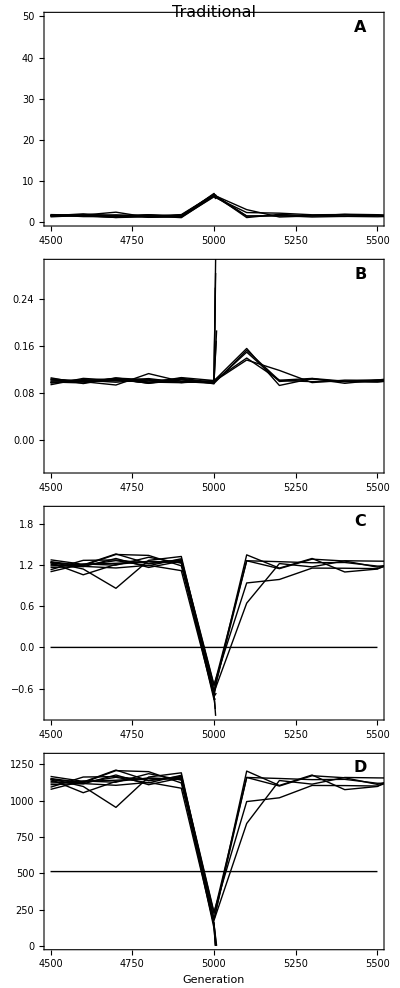

```mathematica
(*parameter values*)
KK=512;
B=3;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
k=0.1;
σθ=0;

burngens=1000;
genjump=5000; (*time when optimum jumps*)
jumpsize=5; (*amt by which optimum jumps*)
maxrep=9;(*number of replicates minus 1*)
mintime=genjump-500;
maxtime=genjump+500;

(*directory and sim name*)
datadir=simdir<>"tradhysteresis/";
Clear[sim]
sim[i_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_k"<>ToString[NumberForm[k,{2,2}]]<>"_rep"<>ToString[i]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[i_]:=gens[i]=Import[datadir<>"gens_"<>sim[i]];
genos[i_]:=genos[i]=Import[datadir<>"genos_"<>sim[i]];
phenos[i_]:=phenos[i]=Import[datadir<>"phenos_"<>sim[i]];
ns[i_]:=ns[i]=Import[datadir<>"n_"<>sim[i]];
numparents[i_]:=numparents[i]=Import[datadir<>"numparents_"<>sim[i]];

(*indices to plot*)
Clear[imin,imax]
imin[i_]:=imin[i]=Position[gens[i][[1]],mintime][[1]][[1]]
imax[i_]:=imax[i]=Max[Position[gens[i][[1]],maxtime][[1]][[1]],Length[gens[i][[1]]]]

(*mean phenotypic lag*)
plot1=Show[
(*Plot[Max[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L] ],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Gray,Thick,Dashing[Large]},Axes->False],
Plot[Min[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L] ],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[Max[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L]] ,{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Gray,Thick,Dotted}],
Plot[Min[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L] ],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted}],*)
Table[ListPlot[Table[{gens[i][[1,j]],If[gens[i][[1,j]]<genjump,k (gens[i][[1,j]]-burngens)-Mean[phenos[i][[j]]],k (gens[i][[1,j]]-burngens)+jumpsize-Mean[phenos[i][[j]]]]},{j,imin[i],imax[i]}],Joined->True,PlotStyle->Black,Axes->False],{i,0,maxrep}],
PlotRange->{{mintime,maxtime},{0,50}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Mean lag",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Traditional",LabelSize],Scaled@{0.5,1}]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];


(*(*genetic variance*)
plot2=Show[
Plot[σg^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,
{t,mintime,maxtime},PlotRange->{0,1},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[σg^2/.σg^2->4n μ α^2 Ne/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotRange->{0,0.5},PlotStyle->{Black,Thick,Dotted}],
Table[ListPlot[Table[{gens[i][[1,j]],Variance[genos[i][[j]]]},{j,imin[i],imax[i]}],Joined->True,PlotStyle->Black],{i,0,maxrep}],
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];*)

(*rate of evo*)
plot2=Show[
Table[ListPlot[Table[{gens[i][[1,j]],(Mean[genos[i][[j]]]-Mean[genos[i][[j-1]]])/(gens[i][[1,j]]-gens[i][[1,j-1]])},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},All},Axes->False,PlotStyle->Black],{i,0,maxrep}],
(*Plot[σg^2/(√ⅇ ω)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Black,Thick,Dashing[Large]}],
Plot[σg^2/(√ⅇ ω)/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Black,Thick,Dotted}],*)
PlotRange->{{mintime,maxtime},{-0.05,0.30}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Rate of evolution",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*popn growth rate*)
plot3=Show[
Table[ListPlot[Table[{gens[i][[1,j]],ns[i][[1,j]]/numparents[i][[1,j]]-1},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},{-1,2}},Axes->False,PlotStyle->Black],{i,0,maxrep}],
Plot[0,{t,mintime,maxtime},PlotStyle->{Black,Thick}],
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Population growth rate",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*survivors of viability selection*)
plot4=Show[
Table[ListPlot[Table[{gens[i][[1,j]],ns[i][[1,j]]},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},{0,1300}},Axes->False,PlotStyle->Black, PlotRangeClipping->True],{i,0,maxrep}],
Plot[KK,{t,mintime,maxtime},PlotStyle->{Black,Thick}],
(*Plot[(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Thick,Black}],*)
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Generation",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Number of surviving offspring",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Black,Black}},
PlotRangeClipping->False
];

GraphicsGrid[{{plot1},{plot2},{plot3},{plot4}(*,{plot5}*)},ImageSize->FigureSize,Spacings->0]

Export[imagedir<>"TradHysteresisSnapshotLarge.pdf",%];

Clear[KK,B,ω,μ,α,n,k,rep,σθ]
```

#### Figure 4 (E-F): hysteresis snapshot (alternative)

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

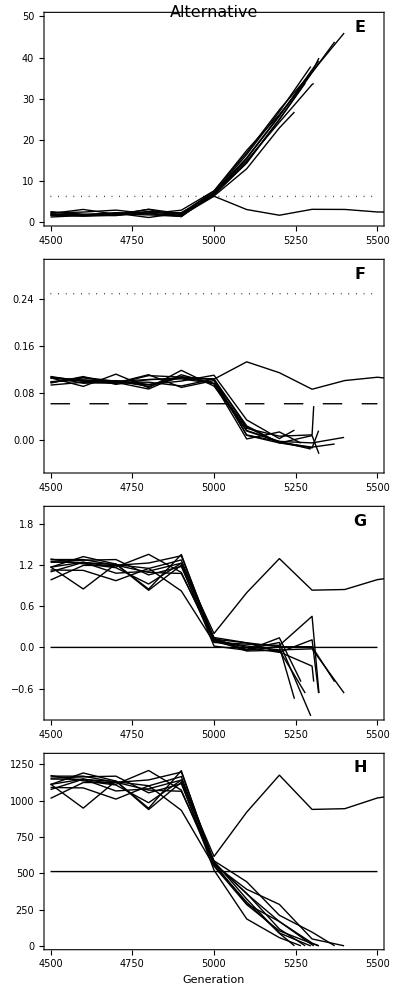

```mathematica
(*parameter values*)
KK=512;
B=3;
ω=3;
μ=0.0002;
α=0.05^(1/2);
n=50;
k=0.1;
σθ=0;

burngens=1000;
genjump=5000; (*time when optimum jumps*)
jumpsize=5; (*amt by which optimum jumps*)
maxrep=9;(*number of replicates minus 1*)
mintime=genjump-500;
maxtime=genjump+500;

(*directory and sim name*)
datadir=simdir<>"althysteresis/";
Clear[sim]
sim[i_]:="K"<>ToString[KK]<>"_B"<>ToString[B]<>"_w"<>ToString[ω]<>"_u"<>ToString[μ]<>"_alphasqrd"<>ToString[α^2]<>"_n"<>ToString[n]<>"_k"<>ToString[NumberForm[k,{2,2}]]<>"_rep"<>ToString[i]<>".csv";

(*simulation results*)
Clear[gens,genos,phenos,ns,numparents]
gens[i_]:=gens[i]=Import[datadir<>"gens_"<>sim[i]];
genos[i_]:=genos[i]=Import[datadir<>"genos_"<>sim[i]];
phenos[i_]:=phenos[i]=Import[datadir<>"phenos_"<>sim[i]];
ns[i_]:=ns[i]=Import[datadir<>"n_"<>sim[i]];
numparents[i_]:=numparents[i]=Import[datadir<>"numparents_"<>sim[i]];

(*indices to plot*)
Clear[imin,imax]
imin[i_]:=imin[i]=Position[gens[i][[1]],mintime][[1]][[1]]
imax[i_]:=imax[i]=Max[Position[gens[i][[1]],maxtime][[1]][[1]],Length[gens[i][[1]]]]

(*mean phenotypic lag*)
plot1=Show[
(*Plot[Max[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L] ],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Gray,Thick,Dashing[Large]},Axes->False],
Plot[Min[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L]],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],*)
Plot[Max[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L]] ,{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted},Axes->False],
(*Plot[Min[L/.NSolve[(ⅇ^(-(-barg+θ)^2/(2 ω^2)) (-barg+θ) σg^2)/ω^2==k/.θ->L+barg/.σg->(4n μ α^2 Ne)^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,L] ],{t,mintime,maxtime},PlotRange->{0,All},PlotStyle->{Black,Thick,Dotted}],*)
Table[ListPlot[Table[{gens[i][[1,j]],If[gens[i][[1,j]]<genjump,k (gens[i][[1,j]]-burngens)-Mean[phenos[i][[j]]],k (gens[i][[1,j]]-burngens)+jumpsize-Mean[phenos[i][[j]]]]},{j,imin[i],imax[i]}],Joined->True,PlotStyle->Black,Axes->False],{i,0,maxrep}],
PlotRange->{{mintime,maxtime},{0,50}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Alternative",LabelSize],Scaled@{0.5,1}]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*(*genetic variance*)
plot2=Show[
Plot[σg^2/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,
{t,mintime,maxtime},PlotRange->{0,1},PlotStyle->{Black,Thick,Dashing[Large]},Axes->False],
Plot[σg^2/.σg^2->4n μ α^2 Ne/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotRange->{0,0.5},PlotStyle->{Black,Thick,Dotted}],
Table[ListPlot[Table[{gens[i][[1,j]],Variance[genos[i][[j]]]},{j,imin[i],imax[i]}],Joined->True,PlotStyle->Black],{i,0,maxrep}],
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];*)

(*rate of evo*)
plot2=Show[
Table[ListPlot[Table[{gens[i][[1,j]],(Mean[genos[i][[j]]]-Mean[genos[i][[j-1]]])/(gens[i][[1,j]]-gens[i][[1,j-1]])},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},All},Axes->False,PlotStyle->Black],{i,0,maxrep}],
Plot[σg^2/(√ⅇ ω)/.σg->((4n μ α^2 Ne)/(1+(α^2 Ne)/Vs))^(1/2)/.Vs->ω^2+1/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Black,Thick,Dashing[Large]}],
Plot[σg^2/(√ⅇ ω)/.σg->(4n μ α^2 Ne)^(1/2)/.Ne->(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Black,Thick,Dotted}],
PlotRange->{{mintime,maxtime},{-0.05,0.30}},
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*popn growth rate*)
plot3=Show[
Table[ListPlot[Table[{gens[i][[1,j]],ns[i][[1,j]]/numparents[i][[1,j]]-1},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},{-1,2}},Axes->False,PlotStyle->Black],{i,0,maxrep}],
Plot[0,{t,mintime,maxtime},PlotStyle->{Black,Thick}],
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{"",Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["G",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
PlotRangeClipping->False
];

(*survivors of viability selection*)
plot4=Show[
Table[ListPlot[Table[{gens[i][[1,j]],ns[i][[1,j]]},{j,imin[i],imax[i]}],Joined->True,PlotRange->{{mintime,maxtime},{0,1300}},Axes->False,PlotStyle->Black, PlotRangeClipping->True],{i,0,maxrep}],
Plot[KK,{t,mintime,maxtime},PlotStyle->{Black,Thick}],
(*Plot[(2B)/(2B-1)KK,{t,mintime,maxtime},PlotStyle->{Thick,Black}],*)
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["Generation",LabelSize],Style["",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
Text[Style["H",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
ImagePadding->Pad,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
PlotRangeClipping->False
];

GraphicsGrid[{{plot1},{plot2},{plot3},{plot4}(*,{plot5}*)},ImageSize->FigureSize,Spacings->0]

Export[imagedir<>"AltHysteresisSnapshotLarge.pdf",%];

Clear[KK,B,ω,μ,α,n,k,rep,σθ]
```